# 2-frequency system

Wormholes:
Change Parameters
Comparing Approximations and Numerical

```mathematica
ClearAll[k1,k2,x,phi1,phi2,psi1,psi2,lambdac,h,h0,sol0,bFun,phase,a1,a2,h12,h12A,h12B,h12C,h12D,hA,hB,hC,hD,h12C,h12C,sol0,solA,solB,solC,solD,pltA]
```

```mathematica
imgsize=700;
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

Endpoint for NDSolve

```mathematica
endpoint=800
```

800

```mathematica
bFun[n1_,n2_,zk1_,zk2_,thetam_]:=Sin[2thetam]/4(-(-I)^(n1+n2))(2n1)BesselJ[n1,zk1]BesselJ[n2,zk2]
phase[n1_,n2_,phi1_,phi2_]:=Exp[I(n1 phi1+n2 phi2)]
```

```mathematica
h1[n1_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=k1/Cos[2thetam] bFun[n1,n2p,zk1,zk2,thetam]phase[n1,n2p,phi1,phi2]Exp[I(n1 k1+n2p k2-1)x]
h2[n2_,n1p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=k2/Cos[2thetam] bFun[n2,n1p,zk2,zk1,thetam]phase[n1p,n2,phi1,phi2]Exp[I(n1p k1+n2 k2-1)x]
```

I have n1 =1, n2=1, n1p=Round[(n2 k2 - 1)/k1], n2p=Round[(n1 k1 - 1)/k2],

```mathematica
thetamV=Pi/5;
k1V=0.35;
k2V=0.95;
a1V=0.1(k2V)^(-5/3);
a2V=0.1(k1V)^(-5/3);
phi1V=0;
phi2V=0;
init={psi1[0],psi2[0]}=={1,0};
```

```mathematica
Print[a1V,a2V]
```

0.1089250.57529

## Numerical Calculations Without Approximations

```mathematica
solN[k1_,k2_,a1_,a2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,n1p1,n2p2,n2p1,n1p2,n1m1,n2m1,n2m2,n1m2,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1M)/k2M];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2M)/k1M];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1M)/k2M];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1M)/k2M];
h=(a1M Sin[k1M x+phi1V]+a2M Sin[k2M x+phi2V])Sin[2thetamV]Exp[I(-x-Cos[2thetamV](a1M/k1M Cos[k1M x+phi1V]+a2M/k2M Cos[k2M x+phi2V]))]/2;
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
pltN[k1_,k2_,a1_,a2_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.solN[k1,k2,a1,a2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->{Dotted,color},PlotLegends->Placed[Style["Numerical;",color],{Top,Center}]]
```

```mathematica
pltN[k1V,k2V,a1V,a2V,Red]
```

-Graphics-

## Approximations

“Most Important” Terms

Include only the “most important” term in the series

```mathematica
sol0[k1_,k2_,a1_,a2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,n1p1,n2p2,n2p1,n1p2,n1m1,n2m1,n2m2,n1m2,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1M)/k2M];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2M)/k1M];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1M)/k2M];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1M)/k2M];
h=h1[n101,n201,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x];
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
plt0[k1_,k2_,a1_,a2_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol0[k1,k2,a1,a2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style["Lowest Order;",color],{Top,Center}]]
```

```mathematica
plt0[k1V,k2V,a1V,a2V,Blue]
```

-Graphics-

Add Corrections of First Frequency

```mathematica
sol01[k1_,k2_,a1_,a2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,n1p1,n2p2,n2p1,n1p2,n1m1,n2m1,n2m2,n1m2,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1M)/k2M];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2M)/k1M];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1M)/k2M];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1M)/k2M];
h=h1[n101,n201,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n1p1,n2p1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n1m1,n2m1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x];
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
plt01[k1_,k2_,a1_,a2_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol01[k1,k2,a1,a2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style["+O(1) in k1;",color],{Top,Center}]]
```

```mathematica
plt01[k1V,k2V,a1V,a2V,Black]
```

-Graphics-

Add Corrections of Second Frequency

```mathematica
sol02[k1_,k2_,a1_,a2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,n1p1,n2p2,n2p1,n1p2,n1m1,n2m1,n2m2,n1m2,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1M)/k2M];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2M)/k1M];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1M)/k2M];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1M)/k2M];
h=h1[n101,n201,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n2p2,n1p2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n2m2,n1m2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x];
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
plt02[k1_,k2_,a1_,a2_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol02[k1,k2,a1,a2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style["+O(1) in k2;",color],{Top,Center}]]
```

```mathematica
plt02[k1V,k2V,a1V,a2V,Gray]
```

-Graphics-

Add Corrections of Both Frequencies

```mathematica
sol012[k1_,k2_,a1_,a2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,n1p1,n2p2,n2p1,n1p2,n1m1,n2m1,n2m2,n1m2,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
n1p1=n101+1;
n2p1=Round[(1-n1p1 k1M)/k2M];
n2p2=n202+1;
n1p2=Round[(1-n2p2 k2M)/k1M];
n1m1=n101-1;
n2m1=Round[(1-n1m1 k1M)/k2M];
n2m2=n202-1;
n1m2=Round[(1-n2m2 k1M)/k2M];
h=h1[n101,n201,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n2p2,n1p2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n2m2,n1m2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n1p1,n2p1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n1m1,n2m1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x];
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
plt012[k1_,k2_,a1_,a2_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol012[k1,k2,a1,a2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style["+O(1) in k1, k2;",color],{Top,Center}]]
```

```mathematica
plt012[k1V,k2V,a1V,a2V,Magenta]
```

-Graphics-

```mathematica
compApproxNum[0.3,0.7,0.1,0.1]
```

compApproxNum[0.3,0.7,0.1,0.1]

Comparing Approximations and Numerical

```mathematica
compApproxNum[k1_,k2_,a1_,a2_]:=Show[pltN[k1,k2,a1,a2,Red],plt0[k1,k2,a1,a2,Blue],plt01[k1,k2,a1,a2,Black],plt02[k1,k2,a1,a2,Gray],plt012[k1,k2,a1,a2,Magenta],PlotRange->All]
(*Why do plt0 and plt01 overlap?*)
```

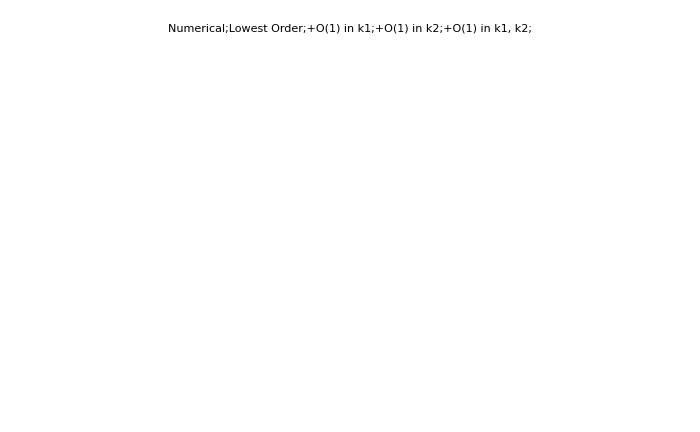

```mathematica
compApproxNum[k1V,k2V,a1V,a2V]
```

```mathematica
expComp[k11_,k21_,k12_,k22_]:=Module[{k11M,k21M,k12M,k22M},
k11M=k11;
k21M=k21;
k12M=k12;
k22M=k22;
Grid[{{compApproxNum[k11M,k21M,0.1(k21M)^(-5/3),0.1(k11M)^(-5/3)],compApproxNum[k11M,k21M,0.1(k11M)^(-5/3),0.1(k21M)^(-5/3)]},{compApproxNum[k12M,k22M,0.1(k12M)^(-5/3),0.1(k22M)^(-5/3)],compApproxNum[k12M,k22M,0.1(k22M)^(-5/3),0.1(k12M)^(-5/3)]}}]
]
```

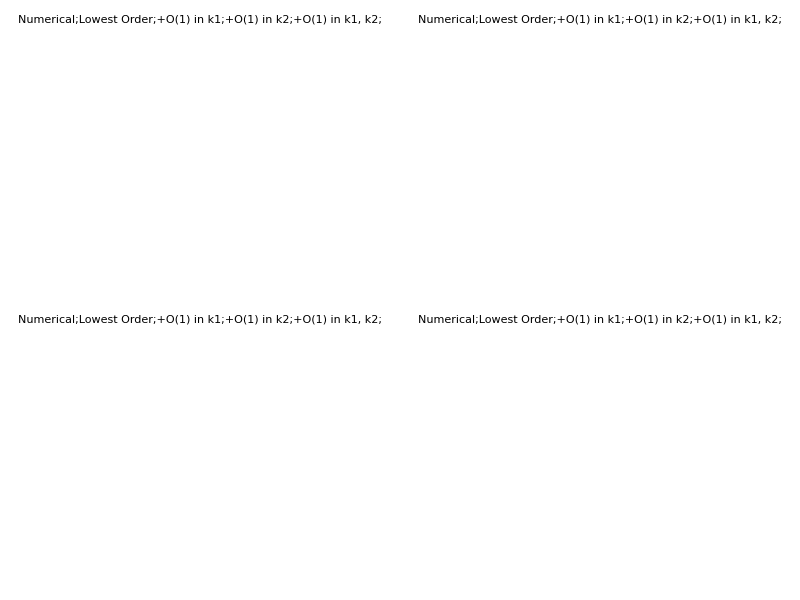

```mathematica
expComp[0.95,1.72,0.7,0.95]
(*Export["export/compApproxNum/compApproxNum.png",%]*)
```

## Even Higher Orders?

```mathematica
Total@Total@Table[h1T[n10+i1,n20+i2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2T[n20+i2,n10+i1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x],{i1,0,0},{i2,0,0}]
```

h1T[n10,n20,k1M,k2M,a1M,a2M,zk1M,zk2M,0,0,π/5,x]+h2T[n20,n10,k1M,k2M,a1M,a2M,zk1M,zk2M,0,0,π/5,x]

```mathematica
sol0Orders[k1_,k2_,a1_,a2_,order1_,order2_]:=Module[{k1M,k2M,a1M,a2M,zk1M,zk2M,n101,n201,n202,n102,h},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
zk1M=a1M Cos[2thetamV]/k1M;
zk2M=a2M Cos[2thetamV]/k2M;
n101=Round[1/k1M];
n201=Round[(1-n101 k1M)/k2M];
n202=Round[1/k2M];
n102=Round[(1-n202 k2M)/k1M];
h=Total@Total@Table[h1[n101+i1,n201+i2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x],{i1,-order1,order1},{i2,-order2,order2}]+Total@Total@Table[h2[n202+i1,n102+i2,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x],{i1,-order1,order1},{i2,-order2,order2}];
(*h=h1[n101,n201,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102+1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h2[n202,n102-1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n101,n201+1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x]+h1[n101,n201-1,k1M,k2M,a1M,a2M,zk1M,zk2M,phi1V,phi2V,thetamV,x];
*)NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
plt0Orders[k1_,k2_,a1_,a2_,order1_,order2_,legends_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol0Orders[k1,k2,a1,a2,order1,order2]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}]]
Module[{k1,k2,a1,a2},
k1=0.95;
k2=1.55;
a1=0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);
Show[pltN[k1,k2,a1,a2,Red],plt0Orders[k1,k2,a1,a2,0,0,"Lowest Order;",Blue],plt0Orders[k1,k2,a1,a2,0,1,"0,1;",Magenta],PlotRange->All]
]
```

-Graphics-

## All Orders of the other frequency

```mathematica
h1All[n1_,k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=-k1 Tan[2thetam]/2((-I)^(n1))(n1)BesselJ[n1,a1/k1 Cos[2thetam]]Exp[I n1 phi1]Exp[I(n1 k1-1)x]Exp[-I a2/k2 Cos[2thetam]Cos[k2 x + phi2]]
h2All[n2_,k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=-k2 Tan[2thetam]/2(-I)^(n2)n2 BesselJ[n2,a2/k2 Cos[2thetam]]Exp[I(n2 k2-1)x]Exp[I n2 phi2]Exp[-I a1/k1 Cos[2thetam]Cos[k1 x+phi1]]
```

```mathematica
solAll[k1_,k2_,a1_,a2_,order_]:=Module[{k1M,k2M,a1M,a2M,n10,n20,h,hamilOrder,orderM},
k1M=k1;
k2M=k2;
a1M=a1;
a2M=a2;
n10=Round[1/k1M];
n20=Round[1/k2M];
orderM=order;
h=Total@Table[h1All[n10+i,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20+i,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x],{i,-orderM,orderM}];
(*h=h1All[n10,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h1All[n10-1,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20-1,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h1All[n10+1,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20+1,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h1All[n10-2,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20-2,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h1All[n10+2,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x]+h2All[n20+2,k1M,k2M,a1M,a2M,phi1V,phi2V,thetamV,x];
*)NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h},{Conjugate[h],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]
]
```

```mathematica
pltAll[k1_,k2_,a1_,a2_,order_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.solAll[k1,k2,a1,a2,order]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style["All Order;",color],{Top,Center}]]
```

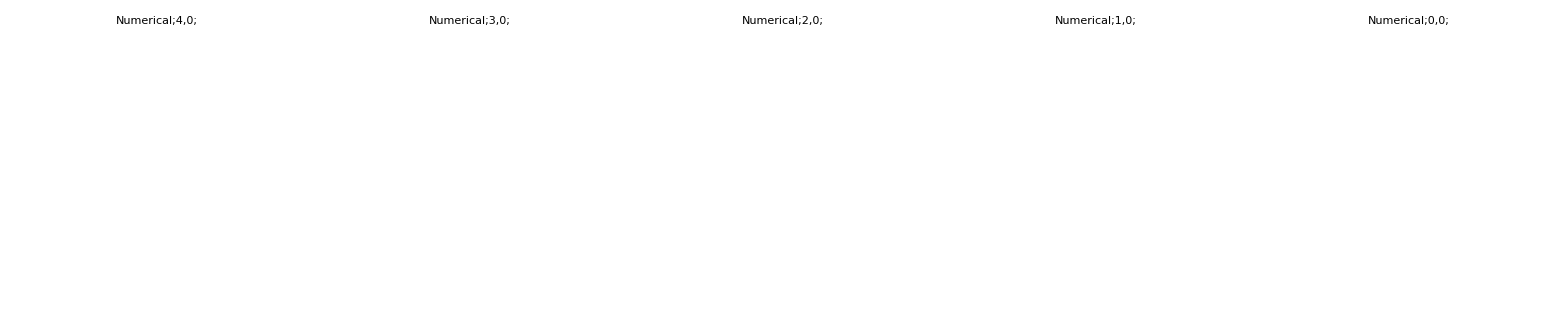

```mathematica
Module[{k1,k2,a1,a2,order},
k1=0.3;
k2=0.99;
a1=0.2*0.1(k1)^(-5/3);
a2=0.1(k2)^(-5/3);
order=4;
Grid@{Table[Show[pltN[k1,k2,a1,a2,Red],plt0Orders[k1,k2,a1,a2,ord,0,ToString[ord]<>",0;",Black](*,pltAll[k1,k2,a1,a2,order,Magenta]*),PlotRange->All],{ord,order,0,-1}]}
]
```

## Analytical

Solve the equation of motion for lowest order

```mathematica
(*ClearAll[sys,psi,psi1,psi2,k,fact1R,fact1I,fact2R,fact2I,helem]
helem=(fact1R+I fact1I)Exp[I(n1 k1+k2p k2 -1)x]+(fact2R+I fact2I)Exp[I(n1p k1+k2 k2 -1)x]
helemConj=(fact1R-I fact1I)Exp[-I(n1 k1+k2p k2 -1)x]+(fact2R-I fact2I)Exp[-I(n1p k1+k2 k2 -1)x]
sys = I D[{psi1[x],psi2[x]},x]=={{0,helem},{helemConj,0}}.{psi1[x],psi2[x]}
DSolve[sys,{psi1,psi2},x]//FullSimplify*)
```